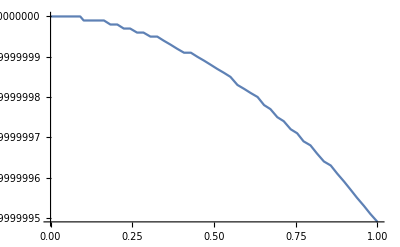

```mathematica
Ztot=(*1/(I w C1)+*)1/(I w C2 + 1/(R+I w L));
(*Simplify[1/Ztot]*)
(*Solve[Simplify[D[(Ztot*Conjugate[Ztot]),w]]==0,w]*)
(*Ztot=1/(I w C1)+I w L + R;*)
rule={L->10 10^-15,
R->0.1,
C1->10 10^-15,
C2->10 10^-15};
(*L=1;
R=1;
C1=20;
C2=1;*)
Plot[Abs[1/Ztot/.rule],{w,0.01,10^8},PlotRange->All]
```